# Recurrence Relationships

An m term linear constant coefficient recurrence
	a_n=c_1 a_(n-1)+c_2 a_(n-2)+…+c_m a_(n-m)
 defines the sequence a_1,a_2,… from initial condition a_1,a_(2,)…,a_m and the coefficients c_1,c_2,…,c_m.   A recurrence is stable if all initial conditions generate sequences that decay to zero.

The BDF formula on the Dahlquist test problem y'=λ y are of this form.  We want to understand when all the solutions of the BDF recurrence decay to zero.  We are looking for a computable condition on the coefficients that ensures all the solutions decay to zero.

## Messing Around

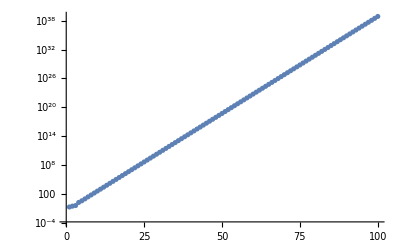

```mathematica
{c1,c2,c3}={1.2,2.1,3.2};
{a1,a2,a3}={0.2,0.3,0.4};
Clear[a]
{a[1],a[2],a[3]}={a1,a2,a3};
a[n_]:=a[n]=c1*a[n-1]+c2*a[n-2]+c3*a[n-3]
ListLogPlot[Table[Abs[a[i]],{i, 1,100}]]
```